```mathematica
Quit[]
```

### preamble

```mathematica
SetDirectory["~/Documents/Univ/StocForm_for_Gauge"]
```

/Users/yuichirotada/Documents/Univ/StocForm_for_Gauge

```mathematica
alpha=1/137;
ee=√(4π alpha);
```

```mathematica
SigmaxiListFujita=Import["Sigmaxi_Fujita.dat"];
SigmaxiListIR=Import["SigmaxiIR.dat"];
```

```mathematica
SigmaFujitaInt[xi_]=Interpolation[SigmaxiListFujita][xi];
SigmaIRint[xi_]=Interpolation[SigmaxiListIR][xi];
```

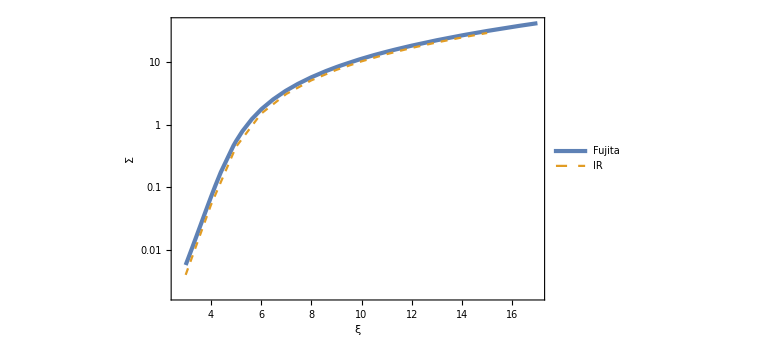

```mathematica
ListLogPlot[{SigmaxiListFujita,SigmaxiListIR},FrameLabel->{ξ,Σ},PlotStyle->{AbsoluteThickness[3],Dashed},PlotLegends->{"Fujita","IR"}]
```

```mathematica
kmaxList=Import["kmaxvsxi.dat"]//ToExpression;
```

```mathematica
kmaxint[xi_]=Interpolation[kmaxList][xi];
```

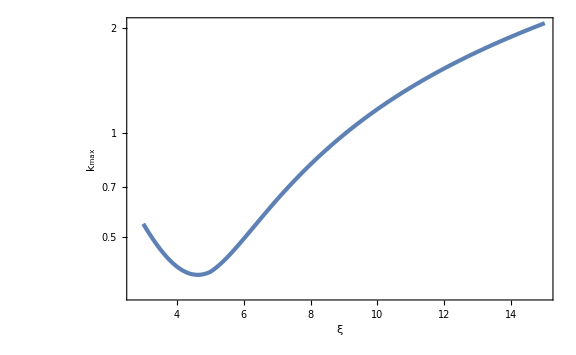

```mathematica
ListLogPlot[kmaxList,FrameLabel->{ξ,Subscript[k, max]}]
```

### Consistent Sigma w/ IR

```mathematica
gamma[xi_]=2xi;
```

```mathematica
HH=10^-5;
```

```mathematica
WW[x_,xi_]=WhittakerW[-I xi,1/2,-2I x];
WS[x_,Sg_,xi_]=WhittakerW[-I xi,(1+Sg)/2,-2I x];
MS[x_,Sg_,xi_]=WhittakerM[-I xi,(1+Sg)/2,-2I x];
Wp[x_,xi_]=D[WW[x,xi], x]//Simplify;
WSp[x_,Sg_,xi_]=D[WS[x,Sg,xi], x]//Simplify;
MSp[x_,Sg_,xi_]=D[MS[x,Sg,xi], x]//Simplify;
```

```mathematica
c2[Sg_,xi_]=gamma[xi]^(-Sg/2)Gamma[1+I xi+Sg/2]/(2I Gamma[Sg+2])(Wp[x,xi]MS[x,Sg,xi]-WW[x,xi]MSp[x,Sg,xi]-Sg/(2gamma[xi])WW[x,xi]MS[x,Sg,xi])/.{x->gamma[xi]};
c1[Sg_,xi_]=-gamma[xi]^(-Sg/2)Gamma[1+I xi+Sg/2]/(2I Gamma[Sg+2])(Wp[x,xi]WS[x,Sg,xi]-WW[x,xi]WSp[x,Sg,xi]-Sg/(2gamma[xi])WW[x,xi]WS[x,Sg,xi])/.{x->gamma[xi]};
```

```mathematica
PBB[kappa_,Sg_,xi_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)Abs[c1[Sg,xi]MS[x,Sg,xi]+c2[Sg,xi]WS[x,Sg,xi]]^2/.{x->kappa};
PEE[kappa_,Sg_,xi_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)Abs[c1[Sg,xi]MSp[x,Sg,xi]+c2[Sg,xi]WSp[x,Sg,xi]+Sg/(2x)(c1[Sg,xi]MS[x,Sg,xi]+c2[Sg,xi]WS[x,Sg,xi])]^2/.{x->kappa};
PBE[kappa_,Sg_,xi_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)(c1[Sg,xi]MS[x,Sg,xi]+c2[Sg,xi]WS[x,Sg,xi]) Conjugate[c1[Sg,xi]MSp[x,Sg,xi]+c2[Sg,xi]WSp[x,Sg,xi]+Sg/(2x)(c1[Sg,xi]MS[x,Sg,xi]+c2[Sg,xi]WS[x,Sg,xi])]/.{x->kappa};
PEB[kappa_,Sg_,xi_]=Conjugate[PBE[kappa,Sg,xi]];
BvarEx[kappa_,Sg_,xi_]=1/4 PBB[kappa,Sg,xi];
EvarEx[kappa_,Sg_,xi_]=1/(4+2Sg)PEE[kappa,Sg,xi]-xi/((2+Sg)(4+Sg))(PBE[kappa,Sg,xi]+PEB[kappa,Sg,xi])+xi^2/((2+Sg)(4+Sg))PBB[kappa,Sg,xi];
```

```mathematica
SigmaEB[EE_,BB_]=ee^3 BB/(6 π^2 HH^2)Coth[(π BB)/EE];
```

consistent xi with use of EIR and BIR

```mathematica
SigmaxiIR=ParallelTable[{xi,sigmainputvsoutput=Table[{10^logsg,kmax=kappa/.FindMaximum[{Log[Abs[PEE[kappa,10^logsg,xi]]],0<kappa<gamma[xi]},{kappa,1}][[2]]//Quiet;
Re[SigmaEB[√EvarEx[kmax,10^logsg,xi],√BvarEx[kmax,10^logsg,xi]]]},{logsg,Log10[SigmaFujitaInt[xi]]-1/2,Log10[SigmaFujitaInt[xi]]+1/2,1/10}];
logsginoutint[sigma_]=Interpolation[MapAt[Log,sigmainputvsoutput,{All,2}]][sigma];
sigma/.FindRoot[logsginoutint[sigma]==Log[sigma],{sigma,SigmaFujitaInt[xi]}]},{xi,3,15}];//AbsoluteTiming
```

{286.889,Null}

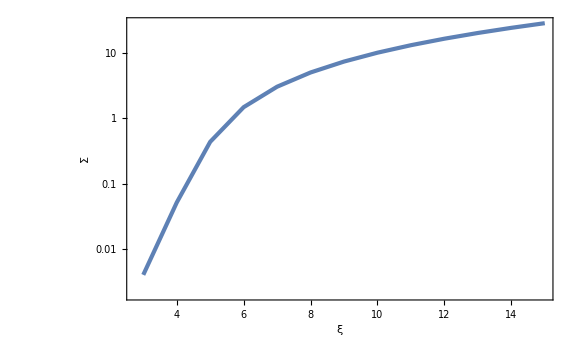

```mathematica
ListLogPlot[SigmaxiIR,FrameLabel->{ξ,Σ}]
```

```mathematica
Export["SigmaxiIR.dat",SigmaxiIR];
```

```mathematica
SigmaxiIRint[xi_]=Interpolation[SigmaxiIR][xi];
```

peak scale k_max with consistent xi

```mathematica
kmaxvsxi=ParallelTable[{xi,kappa/.FindMaximum[{Log[Abs[PEE[kappa,SigmaxiIRint[xi],xi]]],0<kappa<gamma[xi]},{kappa,1}][[2]]//Quiet},{xi,3,15,1/10}];//AbsoluteTiming
```

{75.7023,Null}

```mathematica
ListLogPlot[kmaxvsxi,FrameLabel->{ξ,Subscript[k, max]}]
```

-Graphics-

```mathematica
Export["kmaxvsxi.dat",kmaxvsxi];
```

```mathematica
kmaxvsxiint[xi_]=Interpolation[kmaxvsxi][xi];
```

## kappa = 0.1 (const xi)

### xi = 5

```mathematica
kappa=0.1;
xi=5;
gamma=2xi;
```

```mathematica
Sigma=SigmaIRint[xi]
```

0.437202

```mathematica
WW[x_]=WhittakerW[-I xi,1/2,-2I x];
WS[x_,Sg_]=WhittakerW[-I xi,(1+Sg)/2,-2I x];
MS[x_,Sg_]=WhittakerM[-I xi,(1+Sg)/2,-2I x];
Wp[x_]=D[WW[x], x]//Simplify;
WSp[x_,Sg_]=D[WS[x,Sg], x]//Simplify;
MSp[x_,Sg_]=D[MS[x,Sg], x]//Simplify;
```

```mathematica
c2[Sg_]=gamma^(-Sg/2)Gamma[1+I xi+Sg/2]/(2I Gamma[Sg+2])(Wp[x]MS[x,Sg]-WW[x]MSp[x,Sg]-Sg/(2gamma)WW[x]MS[x,Sg])/.{x->gamma};
c1[Sg_]=-gamma^(-Sg/2)Gamma[1+I xi+Sg/2]/(2I Gamma[Sg+2])(Wp[x]WS[x,Sg]-WW[x]WSp[x,Sg]-Sg/(2gamma)WW[x]WS[x,Sg])/.{x->gamma};
```

```mathematica
XX[Sg_]=c1[Sg]MS[kappa,Sg]+c2[Sg]WS[kappa,Sg];
YY[Sg_]=c1[Sg]MSp[kappa,Sg]+c2[Sg]WSp[kappa,Sg]+Sg/(2kappa)(c1[Sg]MS[kappa,Sg]+c2[Sg]WS[kappa,Sg]);
```

```mathematica
RS[Sg_]=1/(√(Abs[XX[Sg]]^2+Abs[YY[Sg]]^2)){{Abs[YY[Sg]],Abs[XX[Sg]]},{-Abs[XX[Sg]],Abs[YY[Sg]]}};
RT[Sg_]=Transpose[RS[Sg]];
```

```mathematica
HH=10^-5;
```

```mathematica
Amp[Sg_]=kappa^(4+Sg)HH^4/(12 π^2)Exp[π xi](Abs[XX[Sg]]^2+Abs[YY[Sg]]^2);
```

```mathematica
SDE={ⅆBx[t]+2 Bx[t]ⅆt==RT[Sigma][[1,2]] √Amp[Sigma] ⅆwx[t],ⅆBy[t]+2 By[t]ⅆt==RT[Sigma][[1,2]] √Amp[Sigma] ⅆwy[t],ⅆBz[t]+2 Bz[t]ⅆt==RT[Sigma][[1,2]] √Amp[Sigma] ⅆwz[t],ⅆEx[t]+2 Ex[t]ⅆt+2xi Bx[t]ⅆt+Sigma Ex[t]ⅆt==RT[Sigma][[2,2]] √Amp[Sigma] ⅆwx[t],ⅆEy[t]+2 Ey[t]ⅆt+2xi By[t]ⅆt+Sigma Ey[t]ⅆt==RT[Sigma][[2,2]] √Amp[Sigma] ⅆwy[t],ⅆEz[t]+2 Ez[t]ⅆt+2xi Bz[t]ⅆt+Sigma Ez[t] ⅆt==RT[Sigma][[2,2]] √Amp[Sigma] ⅆwz[t]};
```

```mathematica
proc=ItoProcess[SDE,{Bx[t],By[t],Bz[t],Ex[t],Ey[t],Ez[t]},{{Bx,By,Bz,Ex,Ey,Ez},{10^-20,0,0,-10^-20,0,0}},t,{wx\[Distributed]WienerProcess[],wy\[Distributed]WienerProcess[],wz\[Distributed]WienerProcess[]}];
```

```mathematica
Nf=20;
```

```mathematica
sol=RandomFunction[proc,{0,Nf,0.001}];//AbsoluteTiming
```

{0.235653,Null}

```mathematica
Bsol[t_]={sol["PathComponent",1]["PathFunction"][t],sol["PathComponent",2]["PathFunction"][t],sol["PathComponent",3]["PathFunction"][t]};
Esol[t_]={sol["PathComponent",4]["PathFunction"][t],sol["PathComponent",5]["PathFunction"][t],sol["PathComponent",6]["PathFunction"][t]};
```

```mathematica
BAmp[t_]=Norm[Bsol[t]]^2;
NormB[t_]=Bsol[t]/Norm[Bsol[t]];
EAmp[t_]=Norm[Esol[t]]^2;
NormE[t_]=Esol[t]/Norm[Esol[t]];
```

```mathematica
PBB[Sg_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)Abs[c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg]]^2/.{x->kappa};
PEE[Sg_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)Abs[c1[Sg]MSp[x,Sg]+c2[Sg]WSp[x,Sg]+Sg/(2x)(c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg])]^2/.{x->kappa};
PBE[Sg_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)(c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg]) Conjugate[c1[Sg]MSp[x,Sg]+c2[Sg]WSp[x,Sg]+Sg/(2x)(c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg])]/.{x->kappa};
PEB[Sg_]=Conjugate[PBE[Sg]];
BvarEx[Sg_]=1/4 PBB[Sg];
EvarEx[Sg_]=1/(4+2Sg)PEE[Sg]-xi/((2+Sg)(4+Sg))(PBE[Sg]+PEB[Sg])+xi^2/((2+Sg)(4+Sg))PBB[Sg];
EdotBNorm[Sg_]=(1/(4+Sg)Re[PEB[Sg]]-xi/(2(4+Sg))PBB[Sg])/(√(BvarEx[Sg]EvarEx[Sg]));
```

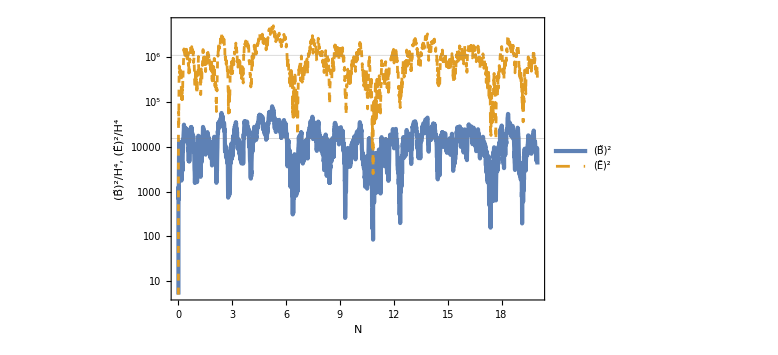

```mathematica
LogPlot[{BAmp[t]/HH^4,EAmp[t]/HH^4},{t,0,Nf},GridLines->{None,{BvarEx[Sigma]/HH^4,Abs[EvarEx[Sigma]]/HH^4}},PlotStyle->{AbsoluteThickness[3],{AbsoluteThickness[2],Dashed}},FrameLabel->{N,Row[{OverTilde[Style[B,Bold]]^2,"/",Superscript[H,4],",  ",OverTilde[Style["E",Italic,Bold]]^2,"/",Superscript[H,4]}]},PlotLegends->Placed[LineLegend[{OverTilde[Style[B,Bold]]^2,OverTilde[Style["E",Italic,Bold]]^2},LegendMarkerSize->20,LegendLayout->"Row",LegendFunction->(Framed[#,Background->White]&)],{0.8,0.15}]]
```

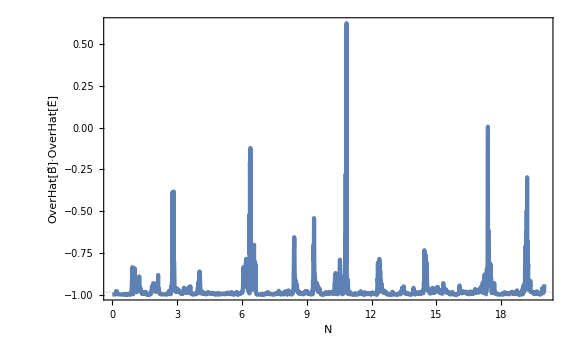

```mathematica
Plot[NormB[t].NormE[t],{t,0,Nf},PlotRange->Full,FrameLabel->{N,OverHat[OverTilde[Style[B,Bold]]]·OverHat[OverTilde[Style["E",Italic,Bold]]]},GridLines->{None,{Re[EdotBNorm[Sigma]]}}]
```

```mathematica
Nplot=12;
ParametricPlot3D[{NormB[t],NormE[t]},{t,Nplot,Nplot+1},AxesLabel->{x,y,z},PlotLegends->Placed[{OverHat[OverTilde[Style[B,Bold]]],OverHat[OverTilde[Style["E",Italic,Bold]]]},{0.1,0.1}],PlotLabel->Style[Row[{N==Nplot,"–",Nplot+1}],Black,Large,FontFamily->"Palatino"]]
```

-Graphics-

```mathematica
MolTheta[phi_]:=theta/.FindRoot[π Sin[phi]==Sin[2theta]+2theta,{theta,0}]
MolPoint[lambda_,phi_]:={lambda Cos[MolTheta[phi]],π/2 Sin[MolTheta[phi]]}
```

```mathematica
lambdaB[t_]=Sign[Bsol[t][[2]]]ArcCos[(Bsol[t][[1]])/(√((Bsol[t][[1]])^2+(Bsol[t][[2]])^2))];
phiB[t_]=ArcSin[NormB[t][[3]]];
MolB[t_]:=MolPoint[lambdaB[t],phiB[t]]
lambdaE[t_]=Sign[Esol[t][[2]]]ArcCos[(Esol[t][[1]])/(√((Esol[t][[1]])^2+(Esol[t][[2]])^2))];
phiE[t_]=ArcSin[NormE[t][[3]]];
MolE[t_]:=MolPoint[lambdaE[t],phiE[t]]
```

```mathematica
MolLongList=Table[MolPoint[lambda,phi],{lambda,-π,π,π/18},{phi,-π/2,π/2,π/180}];//AbsoluteTiming
MolLatList=Table[MolPoint[lambda,phi],{phi,-π/2,π/2,π/18},{lambda,-π,π,π/180}];//AbsoluteTiming
MolFrameList={Table[MolPoint[-π,phi],{phi,-π/2,π/2,π/180}],Table[MolPoint[π,phi],{phi,-π/2,π/2,π/180}]};
```

{9.75191,Null}

{9.8351,Null}

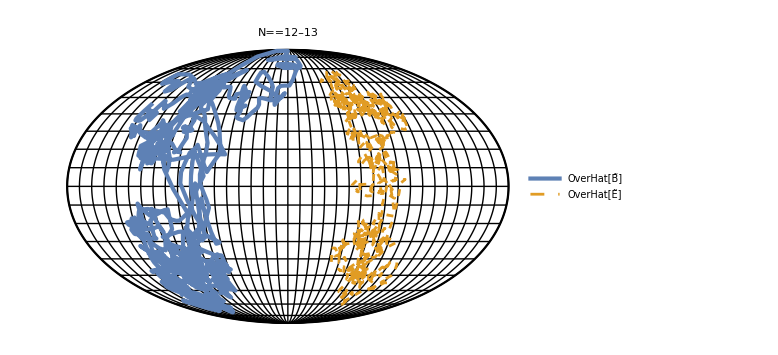

```mathematica
Nplot=12;
Show[ListPlot[MolLongList,PlotStyle->{{Thin,Black}},Frame->False,Axes->False],ListPlot[MolLatList,PlotStyle->{{Thin,Black}}],ListPlot[MolFrameList,PlotStyle->{Black}],ParametricPlot[{MolB[t],MolE[t]},{t,Nplot,Nplot+1},PlotStyle->{AbsoluteThickness[3],{AbsoluteThickness[2],Dashed}},PlotLegends->Placed[LineLegend[{OverHat[OverTilde[Style[B,Bold]]],OverHat[OverTilde[Style["E",Italic,Bold]]]},LegendMarkerSize->20,LabelStyle->Directive[Black,FontSize->20,FontFamily->"Palatino"],LegendFunction->(Framed[#,RoundingRadius->4,Background->White]&)],{0.1,0.2}]],PlotLabel->Style[Row[{N==Nplot,"–",Nplot+1}],Black,Large,FontFamily->"Palatino"],LabelStyle->Directive[Black]]
```

### xi = 10

```mathematica
kappa=0.1;
xi=10;
gamma=2xi;
```

```mathematica
Sigma=SigmaIRint[xi]
```

10.199

```mathematica
WW[x_]=WhittakerW[-I xi,1/2,-2I x];
WS[x_,Sg_]=WhittakerW[-I xi,(1+Sg)/2,-2I x];
MS[x_,Sg_]=WhittakerM[-I xi,(1+Sg)/2,-2I x];
Wp[x_]=D[WW[x], x]//Simplify;
WSp[x_,Sg_]=D[WS[x,Sg], x]//Simplify;
MSp[x_,Sg_]=D[MS[x,Sg], x]//Simplify;
```

```mathematica
c2[Sg_]=gamma^(-Sg/2)Gamma[1+I xi+Sg/2]/(2I Gamma[Sg+2])(Wp[x]MS[x,Sg]-WW[x]MSp[x,Sg]-Sg/(2gamma)WW[x]MS[x,Sg])/.{x->gamma};
c1[Sg_]=-gamma^(-Sg/2)Gamma[1+I xi+Sg/2]/(2I Gamma[Sg+2])(Wp[x]WS[x,Sg]-WW[x]WSp[x,Sg]-Sg/(2gamma)WW[x]WS[x,Sg])/.{x->gamma};
```

```mathematica
XX[Sg_]=c1[Sg]MS[kappa,Sg]+c2[Sg]WS[kappa,Sg];
YY[Sg_]=c1[Sg]MSp[kappa,Sg]+c2[Sg]WSp[kappa,Sg]+Sg/(2kappa)(c1[Sg]MS[kappa,Sg]+c2[Sg]WS[kappa,Sg]);
```

```mathematica
RS[Sg_]=1/(√(Abs[XX[Sg]]^2+Abs[YY[Sg]]^2)){{Abs[YY[Sg]],Abs[XX[Sg]]},{-Abs[XX[Sg]],Abs[YY[Sg]]}};
RT[Sg_]=Transpose[RS[Sg]];
```

```mathematica
HH=10^-5;
```

```mathematica
Amp[Sg_]=kappa^(4+Sg)HH^4/(12 π^2)Exp[π xi](Abs[XX[Sg]]^2+Abs[YY[Sg]]^2);
```

```mathematica
SDE={ⅆBx[t]+2 Bx[t]ⅆt==RT[Sigma][[1,2]] √Amp[Sigma] ⅆwx[t],ⅆBy[t]+2 By[t]ⅆt==RT[Sigma][[1,2]] √Amp[Sigma] ⅆwy[t],ⅆBz[t]+2 Bz[t]ⅆt==RT[Sigma][[1,2]] √Amp[Sigma] ⅆwz[t],ⅆEx[t]+2 Ex[t]ⅆt+2xi Bx[t]ⅆt+Sigma Ex[t]ⅆt==RT[Sigma][[2,2]] √Amp[Sigma] ⅆwx[t],ⅆEy[t]+2 Ey[t]ⅆt+2xi By[t]ⅆt+Sigma Ey[t]ⅆt==RT[Sigma][[2,2]] √Amp[Sigma] ⅆwy[t],ⅆEz[t]+2 Ez[t]ⅆt+2xi Bz[t]ⅆt+Sigma Ez[t] ⅆt==RT[Sigma][[2,2]] √Amp[Sigma] ⅆwz[t]};
```

```mathematica
proc=ItoProcess[SDE,{Bx[t],By[t],Bz[t],Ex[t],Ey[t],Ez[t]},{{Bx,By,Bz,Ex,Ey,Ez},{10^-20,0,0,-10^-20,0,0}},t,{wx\[Distributed]WienerProcess[],wy\[Distributed]WienerProcess[],wz\[Distributed]WienerProcess[]}];
```

```mathematica
Nf=20;
```

```mathematica
sol=RandomFunction[proc,{0,Nf,0.001}];//AbsoluteTiming
```

{0.175757,Null}

```mathematica
Bsol[t_]={sol["PathComponent",1]["PathFunction"][t],sol["PathComponent",2]["PathFunction"][t],sol["PathComponent",3]["PathFunction"][t]};
Esol[t_]={sol["PathComponent",4]["PathFunction"][t],sol["PathComponent",5]["PathFunction"][t],sol["PathComponent",6]["PathFunction"][t]};
```

```mathematica
BAmp[t_]=Norm[Bsol[t]]^2;
NormB[t_]=Bsol[t]/Norm[Bsol[t]];
EAmp[t_]=Norm[Esol[t]]^2;
NormE[t_]=Esol[t]/Norm[Esol[t]];
```

```mathematica
PBB[Sg_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)Abs[c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg]]^2/.{x->kappa};
PEE[Sg_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)Abs[c1[Sg]MSp[x,Sg]+c2[Sg]WSp[x,Sg]+Sg/(2x)(c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg])]^2/.{x->kappa};
PBE[Sg_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)(c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg]) Conjugate[c1[Sg]MSp[x,Sg]+c2[Sg]WSp[x,Sg]+Sg/(2x)(c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg])]/.{x->kappa};
PEB[Sg_]=Conjugate[PBE[Sg]];
BvarEx[Sg_]=1/4 PBB[Sg];
EvarEx[Sg_]=1/(4+2Sg)PEE[Sg]-xi/((2+Sg)(4+Sg))(PBE[Sg]+PEB[Sg])+xi^2/((2+Sg)(4+Sg))PBB[Sg];
EdotBNorm[Sg_]=(1/(4+Sg)Re[PEB[Sg]]-xi/(2(4+Sg))PBB[Sg])/(√(BvarEx[Sg]EvarEx[Sg]));
```

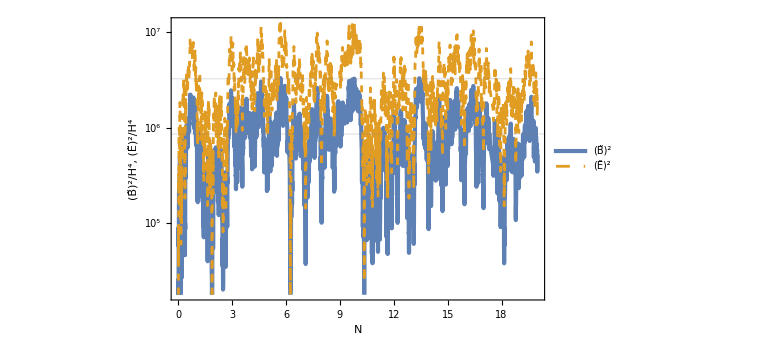

```mathematica
LogPlot[{BAmp[t]/HH^4,EAmp[t]/HH^4},{t,0,Nf},GridLines->{None,{BvarEx[Sigma]/HH^4,Abs[EvarEx[Sigma]]/HH^4}},PlotStyle->{AbsoluteThickness[3],{AbsoluteThickness[2],Dashed}},FrameLabel->{N,Row[{OverTilde[Style[B,Bold]]^2,"/",Superscript[H,4],",  ",OverTilde[Style["E",Italic,Bold]]^2,"/",Superscript[H,4]}]},PlotLegends->Placed[LineLegend[{OverTilde[Style[B,Bold]]^2,OverTilde[Style["E",Italic,Bold]]^2},LegendMarkerSize->20,LegendLayout->"Row",LegendFunction->(Framed[#,Background->White]&)],{0.8,0.15}]]
```

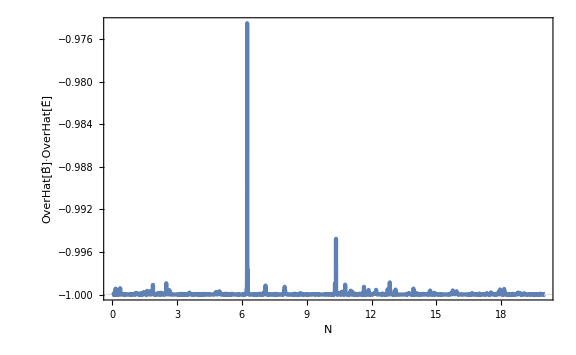

```mathematica
Plot[NormB[t].NormE[t],{t,0,Nf},PlotRange->Full,FrameLabel->{N,OverHat[OverTilde[Style[B,Bold]]]·OverHat[OverTilde[Style["E",Italic,Bold]]]},GridLines->{None,{Re[EdotBNorm[Sigma]]}}]
```

```mathematica
Nplot=16;
ParametricPlot3D[{NormB[t],NormE[t]},{t,Nplot,Nplot+1},AxesLabel->{x,y,z},PlotLegends->Placed[{OverHat[OverTilde[Style[B,Bold]]],OverHat[OverTilde[Style["E",Italic,Bold]]]},{0.1,0.1}],PlotLabel->Style[Row[{N==Nplot,"–",Nplot+1}],Black,Large,FontFamily->"Palatino"]]
```

-Graphics-

```mathematica
MolTheta[phi_]:=theta/.FindRoot[π Sin[phi]==Sin[2theta]+2theta,{theta,0}]
MolPoint[lambda_,phi_]:={lambda Cos[MolTheta[phi]],π/2 Sin[MolTheta[phi]]}
```

```mathematica
lambdaB[t_]=Sign[Bsol[t][[2]]]ArcCos[(Bsol[t][[1]])/(√((Bsol[t][[1]])^2+(Bsol[t][[2]])^2))];
phiB[t_]=ArcSin[NormB[t][[3]]];
MolB[t_]:=MolPoint[lambdaB[t],phiB[t]]
lambdaE[t_]=Sign[Esol[t][[2]]]ArcCos[(Esol[t][[1]])/(√((Esol[t][[1]])^2+(Esol[t][[2]])^2))];
phiE[t_]=ArcSin[NormE[t][[3]]];
MolE[t_]:=MolPoint[lambdaE[t],phiE[t]]
```

```mathematica
MolLongList=Table[MolPoint[lambda,phi],{lambda,-π,π,π/18},{phi,-π/2,π/2,π/180}];//AbsoluteTiming
MolLatList=Table[MolPoint[lambda,phi],{phi,-π/2,π/2,π/18},{lambda,-π,π,π/180}];//AbsoluteTiming
MolFrameList={Table[MolPoint[-π,phi],{phi,-π/2,π/2,π/180}],Table[MolPoint[π,phi],{phi,-π/2,π/2,π/180}]};
```

{10.0945,Null}

{10.957,Null}

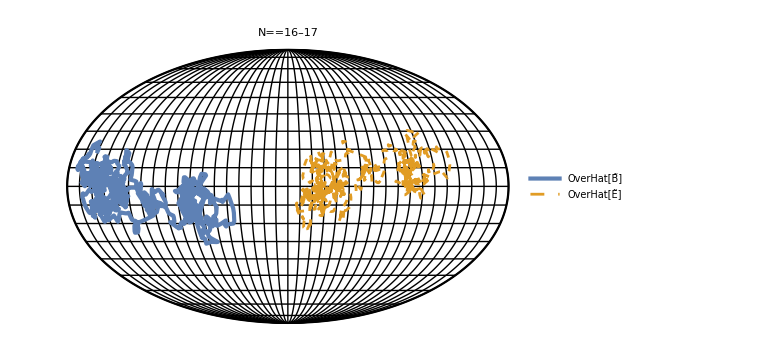

```mathematica
Nplot=16;
Show[ListPlot[MolLongList,PlotStyle->{{Thin,Black}},Frame->False,Axes->False],ListPlot[MolLatList,PlotStyle->{{Thin,Black}}],ListPlot[MolFrameList,PlotStyle->{Black}],ParametricPlot[{MolB[t],MolE[t]},{t,Nplot,Nplot+1},PlotStyle->{AbsoluteThickness[3],{AbsoluteThickness[2],Dashed}},PlotLegends->Placed[LineLegend[{OverHat[OverTilde[Style[B,Bold]]],OverHat[OverTilde[Style["E",Italic,Bold]]]},LegendMarkerSize->20,LabelStyle->Directive[Black,FontSize->20,FontFamily->"Palatino"],LegendFunction->(Framed[#,RoundingRadius->4,Background->White]&)],{0.1,0.2}]],PlotLabel->Style[Row[{N==Nplot,"–",Nplot+1}],Black,Large,FontFamily->"Palatino"],LabelStyle->Directive[Black]]
```

### xi = 15

```mathematica
kappa=0.1;
xi=15;
gamma=2xi;
```

```mathematica
Sigma=SigmaIRint[xi]
```

28.9324

```mathematica
WW[x_]=WhittakerW[-I xi,1/2,-2I x];
WS[x_,Sg_]=WhittakerW[-I xi,(1+Sg)/2,-2I x];
MS[x_,Sg_]=WhittakerM[-I xi,(1+Sg)/2,-2I x];
Wp[x_]=D[WW[x], x]//Simplify;
WSp[x_,Sg_]=D[WS[x,Sg], x]//Simplify;
MSp[x_,Sg_]=D[MS[x,Sg], x]//Simplify;
```

```mathematica
c2[Sg_]=gamma^(-Sg/2)Gamma[1+I xi+Sg/2]/(2I Gamma[Sg+2])(Wp[x]MS[x,Sg]-WW[x]MSp[x,Sg]-Sg/(2gamma)WW[x]MS[x,Sg])/.{x->gamma};
c1[Sg_]=-gamma^(-Sg/2)Gamma[1+I xi+Sg/2]/(2I Gamma[Sg+2])(Wp[x]WS[x,Sg]-WW[x]WSp[x,Sg]-Sg/(2gamma)WW[x]WS[x,Sg])/.{x->gamma};
```

```mathematica
XX[Sg_]=c1[Sg]MS[kappa,Sg]+c2[Sg]WS[kappa,Sg];
YY[Sg_]=c1[Sg]MSp[kappa,Sg]+c2[Sg]WSp[kappa,Sg]+Sg/(2kappa)(c1[Sg]MS[kappa,Sg]+c2[Sg]WS[kappa,Sg]);
```

```mathematica
RS[Sg_]=1/(√(Abs[XX[Sg]]^2+Abs[YY[Sg]]^2)){{Abs[YY[Sg]],Abs[XX[Sg]]},{-Abs[XX[Sg]],Abs[YY[Sg]]}};
RT[Sg_]=Transpose[RS[Sg]];
```

```mathematica
HH=10^-5;
```

```mathematica
Amp[Sg_]=kappa^(4+Sg)HH^4/(12 π^2)Exp[π xi](Abs[XX[Sg]]^2+Abs[YY[Sg]]^2);
```

```mathematica
SDE={ⅆBx[t]+2 Bx[t]ⅆt==RT[Sigma][[1,2]] √Amp[Sigma] ⅆwx[t],ⅆBy[t]+2 By[t]ⅆt==RT[Sigma][[1,2]] √Amp[Sigma] ⅆwy[t],ⅆBz[t]+2 Bz[t]ⅆt==RT[Sigma][[1,2]] √Amp[Sigma] ⅆwz[t],ⅆEx[t]+2 Ex[t]ⅆt+2xi Bx[t]ⅆt+Sigma Ex[t]ⅆt==RT[Sigma][[2,2]] √Amp[Sigma] ⅆwx[t],ⅆEy[t]+2 Ey[t]ⅆt+2xi By[t]ⅆt+Sigma Ey[t]ⅆt==RT[Sigma][[2,2]] √Amp[Sigma] ⅆwy[t],ⅆEz[t]+2 Ez[t]ⅆt+2xi Bz[t]ⅆt+Sigma Ez[t] ⅆt==RT[Sigma][[2,2]] √Amp[Sigma] ⅆwz[t]};
```

```mathematica
proc=ItoProcess[SDE,{Bx[t],By[t],Bz[t],Ex[t],Ey[t],Ez[t]},{{Bx,By,Bz,Ex,Ey,Ez},{10^-20,0,0,-10^-20,0,0}},t,{wx\[Distributed]WienerProcess[],wy\[Distributed]WienerProcess[],wz\[Distributed]WienerProcess[]}];
```

```mathematica
Nf=20;
```

```mathematica
sol=RandomFunction[proc,{0,Nf,0.001}];//AbsoluteTiming
```

{0.17104,Null}

```mathematica
Bsol[t_]={sol["PathComponent",1]["PathFunction"][t],sol["PathComponent",2]["PathFunction"][t],sol["PathComponent",3]["PathFunction"][t]};
Esol[t_]={sol["PathComponent",4]["PathFunction"][t],sol["PathComponent",5]["PathFunction"][t],sol["PathComponent",6]["PathFunction"][t]};
```

```mathematica
BAmp[t_]=Norm[Bsol[t]]^2;
NormB[t_]=Bsol[t]/Norm[Bsol[t]];
EAmp[t_]=Norm[Esol[t]]^2;
NormE[t_]=Esol[t]/Norm[Esol[t]];
```

```mathematica
PBB[Sg_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)Abs[c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg]]^2/.{x->kappa};
PEE[Sg_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)Abs[c1[Sg]MSp[x,Sg]+c2[Sg]WSp[x,Sg]+Sg/(2x)(c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg])]^2/.{x->kappa};
PBE[Sg_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)(c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg]) Conjugate[c1[Sg]MSp[x,Sg]+c2[Sg]WSp[x,Sg]+Sg/(2x)(c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg])]/.{x->kappa};
PEB[Sg_]=Conjugate[PBE[Sg]];
BvarEx[Sg_]=1/4 PBB[Sg];
EvarEx[Sg_]=1/(4+2Sg)PEE[Sg]-xi/((2+Sg)(4+Sg))(PBE[Sg]+PEB[Sg])+xi^2/((2+Sg)(4+Sg))PBB[Sg];
EdotBNorm[Sg_]=(1/(4+Sg)Re[PEB[Sg]]-xi/(2(4+Sg))PBB[Sg])/(√(BvarEx[Sg]EvarEx[Sg]));
```

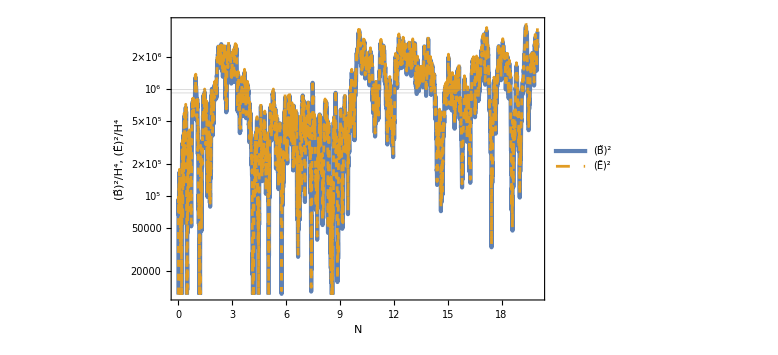

```mathematica
LogPlot[{BAmp[t]/HH^4,EAmp[t]/HH^4},{t,0,Nf},GridLines->{None,{BvarEx[Sigma]/HH^4,Abs[EvarEx[Sigma]]/HH^4}},PlotStyle->{AbsoluteThickness[3],{AbsoluteThickness[2],Dashed}},FrameLabel->{N,Row[{OverTilde[Style[B,Bold]]^2,"/",Superscript[H,4],",  ",OverTilde[Style["E",Italic,Bold]]^2,"/",Superscript[H,4]}]},PlotLegends->Placed[LineLegend[{OverTilde[Style[B,Bold]]^2,OverTilde[Style["E",Italic,Bold]]^2},LegendMarkerSize->20,LegendLayout->"Row",LegendFunction->(Framed[#,Background->White]&)],{0.8,0.15}]]
```

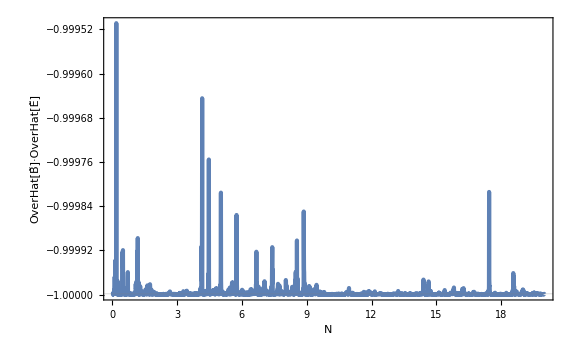

```mathematica
Plot[NormB[t].NormE[t],{t,0,Nf},PlotRange->Full,FrameLabel->{N,OverHat[OverTilde[Style[B,Bold]]]·OverHat[OverTilde[Style["E",Italic,Bold]]]},GridLines->{None,{Re[EdotBNorm[Sigma]]}}]
```

```mathematica
Nplot=14;
ParametricPlot3D[{NormB[t],NormE[t]},{t,Nplot,Nplot+1},AxesLabel->{x,y,z},PlotLegends->Placed[{OverHat[OverTilde[Style[B,Bold]]],OverHat[OverTilde[Style["E",Italic,Bold]]]},{0.1,0.1}],PlotLabel->Style[Row[{N==Nplot,"–",Nplot+1}],Black,Large,FontFamily->"Palatino"]]
```

-Graphics-

```mathematica
MolTheta[phi_]:=theta/.FindRoot[π Sin[phi]==Sin[2theta]+2theta,{theta,0}]
MolPoint[lambda_,phi_]:={lambda Cos[MolTheta[phi]],π/2 Sin[MolTheta[phi]]}
```

```mathematica
lambdaB[t_]=Sign[Bsol[t][[2]]]ArcCos[(Bsol[t][[1]])/(√((Bsol[t][[1]])^2+(Bsol[t][[2]])^2))];
phiB[t_]=ArcSin[NormB[t][[3]]];
MolB[t_]:=MolPoint[lambdaB[t],phiB[t]]
lambdaE[t_]=Sign[Esol[t][[2]]]ArcCos[(Esol[t][[1]])/(√((Esol[t][[1]])^2+(Esol[t][[2]])^2))];
phiE[t_]=ArcSin[NormE[t][[3]]];
MolE[t_]:=MolPoint[lambdaE[t],phiE[t]]
```

```mathematica
MolLongList=Table[MolPoint[lambda,phi],{lambda,-π,π,π/18},{phi,-π/2,π/2,π/180}];//AbsoluteTiming
MolLatList=Table[MolPoint[lambda,phi],{phi,-π/2,π/2,π/18},{lambda,-π,π,π/180}];//AbsoluteTiming
MolFrameList={Table[MolPoint[-π,phi],{phi,-π/2,π/2,π/180}],Table[MolPoint[π,phi],{phi,-π/2,π/2,π/180}]};
```

{10.0945,Null}

{10.957,Null}

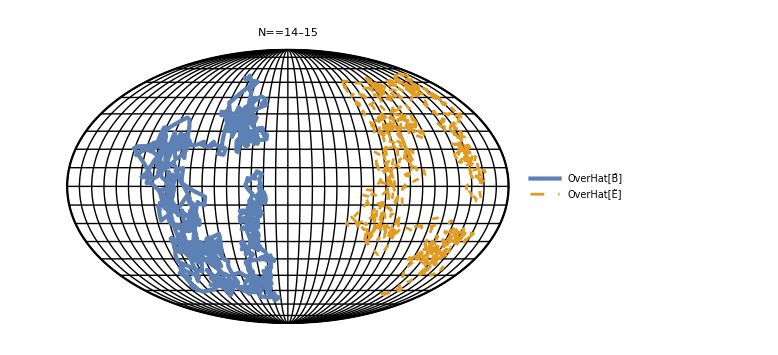

```mathematica
Nplot=14;
Show[ListPlot[MolLongList,PlotStyle->{{Thin,Black}},Frame->False,Axes->False],ListPlot[MolLatList,PlotStyle->{{Thin,Black}}],ListPlot[MolFrameList,PlotStyle->{Black}],ParametricPlot[{MolB[t],MolE[t]},{t,Nplot,Nplot+1},PlotStyle->{AbsoluteThickness[3],{AbsoluteThickness[2],Dashed}},PlotLegends->Placed[LineLegend[{OverHat[OverTilde[Style[B,Bold]]],OverHat[OverTilde[Style["E",Italic,Bold]]]},LegendMarkerSize->20,LabelStyle->Directive[Black,FontSize->20,FontFamily->"Palatino"],LegendFunction->(Framed[#,RoundingRadius->4,Background->White]&)],{0.1,0.2}]],PlotLabel->Style[Row[{N==Nplot,"–",Nplot+1}],Black,Large,FontFamily->"Palatino"],LabelStyle->Directive[Black]]
```

## peak kappa

### xi = 5

```mathematica
xi=5;
gamma=2xi;
kappa=kmaxint[xi]
```

0.397883

```mathematica
HH=10^-5;
```

```mathematica
SigmaEB[EE_,BB_]=ee^3 BB/(6 π^2 HH^2)Coth[(π BB)/EE];
```

```mathematica
WW[x_]=WhittakerW[-I xi,1/2,-2I x];
WS[x_,Sg_]=WhittakerW[-I xi,(1+Sg)/2,-2I x];
MS[x_,Sg_]=WhittakerM[-I xi,(1+Sg)/2,-2I x];
Wp[x_]=D[WW[x], x]//Simplify;
WSp[x_,Sg_]=D[WS[x,Sg], x]//Simplify;
MSp[x_,Sg_]=D[MS[x,Sg], x]//Simplify;
```

```mathematica
c2[Sg_]=gamma^(-Sg/2)Gamma[1+I xi+Sg/2]/(2I Gamma[Sg+2])(Wp[x]MS[x,Sg]-WW[x]MSp[x,Sg]-Sg/(2gamma)WW[x]MS[x,Sg])/.{x->gamma};
c1[Sg_]=-gamma^(-Sg/2)Gamma[1+I xi+Sg/2]/(2I Gamma[Sg+2])(Wp[x]WS[x,Sg]-WW[x]WSp[x,Sg]-Sg/(2gamma)WW[x]WS[x,Sg])/.{x->gamma};
```

```mathematica
XX[Sg_]=c1[Sg]MS[kappa,Sg]+c2[Sg]WS[kappa,Sg];
YY[Sg_]=c1[Sg]MSp[kappa,Sg]+c2[Sg]WSp[kappa,Sg]+Sg/(2kappa)(c1[Sg]MS[kappa,Sg]+c2[Sg]WS[kappa,Sg]);
```

```mathematica
RS[Sg_]=1/(√(Abs[XX[Sg]]^2+Abs[YY[Sg]]^2)){{Abs[YY[Sg]],Abs[XX[Sg]]},{-Abs[XX[Sg]],Abs[YY[Sg]]}};
RT[Sg_]=Transpose[RS[Sg]];
```

```mathematica
Amp[Sg_]=kappa^(4+Sg)HH^4/(12 π^2)Exp[π xi](Abs[XX[Sg]]^2+Abs[YY[Sg]]^2);
```

prepare rotation matrix R and noise amplitude as functions of Sigma (skip it if you already have data)

```mathematica
ListRT12=ParallelTable[{10^logSg,RT[10^logSg][[1,2]]},{logSg,-2,2,1/100}];//AbsoluteTiming
ListRT22=ParallelTable[{10^logSg,RT[10^logSg][[2,2]]},{logSg,-2,2,1/100}];//AbsoluteTiming
ListAmp=ParallelTable[{10^logSg,Amp[10^logSg]},{logSg,-2,2,1/100}];//AbsoluteTiming
```

{597.016,Null}

{475.482,Null}

{81.3505,Null}

```mathematica
Export["RT12xi5_consistentkappa.dat",ListRT12];
Export["RT22xi5_consistentkappa.dat",ListRT22];
Export["Ampxi5_consistentkappa.dat",ListAmp];
```

```mathematica
ListRT12=Import["RT12xi5_consistentkappa.dat"]//ToExpression;
ListRT22=Import["RT22xi5_consistentkappa.dat"]//ToExpression;
ListAmp=Import["Ampxi5_consistentkappa.dat"]//ToExpression;
```

```mathematica
RT12int[Sg_]=Interpolation[ListRT12][Sg];
RT22int[Sg_]=Interpolation[ListRT22][Sg];
Ampint[Sg_]=Interpolation[ListAmp][Sg];
```

```mathematica
SDE={ⅆBx[t]+2 Bx[t]ⅆt==RT12int[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]] Sqrt[Ampint[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]]]ⅆwx[t],ⅆBy[t]+2 By[t]ⅆt==RT12int[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]] Sqrt[Ampint[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]]]ⅆwy[t],ⅆBz[t]+2 Bz[t]ⅆt==RT12int[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]] Sqrt[Ampint[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]]]ⅆwz[t],ⅆEx[t]+2 Ex[t]ⅆt+2xi Bx[t]ⅆt+SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]] Ex[t]ⅆt==RT22int[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]] Sqrt[Ampint[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]]]ⅆwx[t],ⅆEy[t]+2 Ey[t]ⅆt+2xi By[t]ⅆt+SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]] Ey[t]ⅆt==RT22int[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]] Sqrt[Ampint[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]]]ⅆwy[t],ⅆEz[t]+2 Ez[t]ⅆt+2xi Bz[t]ⅆt+SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]] Ez[t] ⅆt==RT22int[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]] Sqrt[Ampint[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]]]ⅆwz[t]};
```

```mathematica
proc=ItoProcess[SDE,{Bx[t],By[t],Bz[t],Ex[t],Ey[t],Ez[t]},{{Bx,By,Bz,Ex,Ey,Ez},{10^-20,0,0,-10^-20,0,0}},t,{wx\[Distributed]WienerProcess[],wy\[Distributed]WienerProcess[],wz\[Distributed]WienerProcess[]}];
```

```mathematica
Nf=20;
```

```mathematica
sol=RandomFunction[proc,{0,Nf,0.001}];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {4.70874×10^-14} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{3.50244,Null}

```mathematica
Bsol[t_]={sol["PathComponent",1]["PathFunction"][t],sol["PathComponent",2]["PathFunction"][t],sol["PathComponent",3]["PathFunction"][t]};
Esol[t_]={sol["PathComponent",4]["PathFunction"][t],sol["PathComponent",5]["PathFunction"][t],sol["PathComponent",6]["PathFunction"][t]};
```

```mathematica
BAmp[t_]=Norm[Bsol[t]]^2;
NormB[t_]=Bsol[t]/Norm[Bsol[t]];
EAmp[t_]=Norm[Esol[t]]^2;
NormE[t_]=Esol[t]/Norm[Esol[t]];
```

```mathematica
PBB[Sg_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)Abs[c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg]]^2/.{x->kappa};
PEE[Sg_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)Abs[c1[Sg]MSp[x,Sg]+c2[Sg]WSp[x,Sg]+Sg/(2x)(c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg])]^2/.{x->kappa};
PBE[Sg_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)(c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg]) Conjugate[c1[Sg]MSp[x,Sg]+c2[Sg]WSp[x,Sg]+Sg/(2x)(c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg])]/.{x->kappa};
PEB[Sg_]=Conjugate[PBE[Sg]];
BvarEx[Sg_]=1/4 PBB[Sg];
EvarEx[Sg_]=1/(4+2Sg)PEE[Sg]-xi/((2+Sg)(4+Sg))(PBE[Sg]+PEB[Sg])+xi^2/((2+Sg)(4+Sg))PBB[Sg];
EdotBNorm[Sg_]=(1/(4+Sg)Re[PEB[Sg]]-xi/(2(4+Sg))PBB[Sg])/(√(BvarEx[Sg]EvarEx[Sg]));
```

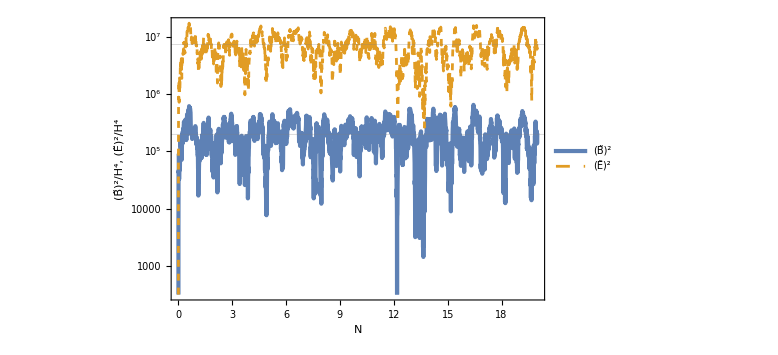

```mathematica
LogPlot[{BAmp[t]/HH^4,EAmp[t]/HH^4},{t,0,Nf},GridLines->{None,{BvarEx[SigmaIRint[xi]]/HH^4,Abs[EvarEx[SigmaIRint[xi]]]/HH^4}},PlotStyle->{AbsoluteThickness[3],{AbsoluteThickness[2],Dashed}},FrameLabel->{N,Row[{OverTilde[Style[B,Bold]]^2,"/",Superscript[H,4],",  ",OverTilde[Style["E",Italic,Bold]]^2,"/",Superscript[H,4]}]},PlotLegends->Placed[LineLegend[{OverTilde[Style[B,Bold]]^2,OverTilde[Style["E",Italic,Bold]]^2},LegendMarkerSize->20,LegendLayout->"Row",LegendFunction->(Framed[#,Background->White]&)],{0.8,0.15}]]
```

```mathematica
SigmaSol[t_]=SigmaEB[Sqrt[EAmp[t]],Sqrt[BAmp[t]]];
```

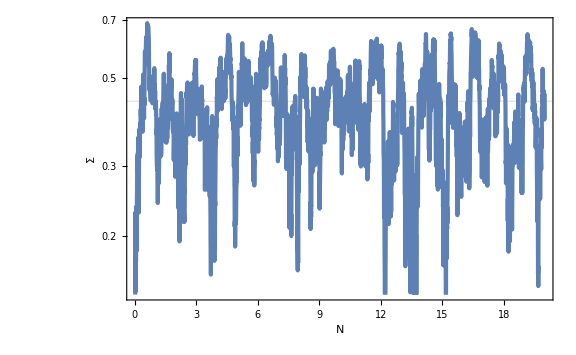

```mathematica
LogPlot[SigmaSol[t],{t,0,Nf},GridLines->{None,{SigmaIRint[xi]}},FrameLabel->{N,Σ}]
```

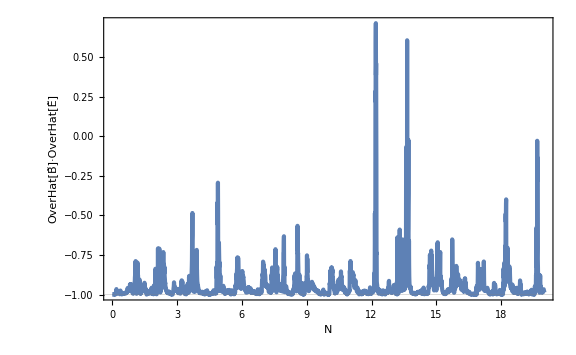

```mathematica
Plot[NormB[t].NormE[t],{t,0,Nf},PlotRange->Full,FrameLabel->{N,OverHat[OverTilde[Style[B,Bold]]]·OverHat[OverTilde[Style["E",Italic,Bold]]]},GridLines->{None,{Re[EdotBNorm[Sigma]]}}]
```

```mathematica
Nplot=7;
ParametricPlot3D[{NormB[t],NormE[t]},{t,Nplot,Nplot+1},AxesLabel->{x,y,z},PlotLegends->Placed[{OverHat[OverTilde[Style[B,Bold]]],OverHat[OverTilde[Style["E",Italic,Bold]]]},{0.1,0.1}],PlotLabel->Style[Row[{N==Nplot,"–",Nplot+1}],Black,Large,FontFamily->"Palatino"]]
```

-Graphics-

```mathematica
MolTheta[phi_]:=theta/.FindRoot[π Sin[phi]==Sin[2theta]+2theta,{theta,0}]
MolPoint[lambda_,phi_]:={lambda Cos[MolTheta[phi]],π/2 Sin[MolTheta[phi]]}
```

```mathematica
lambdaB[t_]=Sign[Bsol[t][[2]]]ArcCos[(Bsol[t][[1]])/(√((Bsol[t][[1]])^2+(Bsol[t][[2]])^2))];
phiB[t_]=ArcSin[NormB[t][[3]]];
MolB[t_]:=MolPoint[lambdaB[t],phiB[t]]
lambdaE[t_]=Sign[Esol[t][[2]]]ArcCos[(Esol[t][[1]])/(√((Esol[t][[1]])^2+(Esol[t][[2]])^2))];
phiE[t_]=ArcSin[NormE[t][[3]]];
MolE[t_]:=MolPoint[lambdaE[t],phiE[t]]
```

```mathematica
MolLongList=Table[MolPoint[lambda,phi],{lambda,-π,π,π/18},{phi,-π/2,π/2,π/180}];//AbsoluteTiming
MolLatList=Table[MolPoint[lambda,phi],{phi,-π/2,π/2,π/18},{lambda,-π,π,π/180}];//AbsoluteTiming
MolFrameList={Table[MolPoint[-π,phi],{phi,-π/2,π/2,π/180}],Table[MolPoint[π,phi],{phi,-π/2,π/2,π/180}]};
```

{6.21984,Null}

{7.2209,Null}

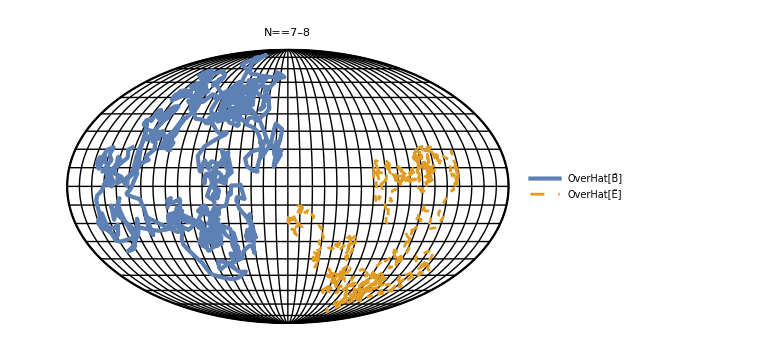

```mathematica
Nplot=7;
Show[ListPlot[MolLongList,PlotStyle->{{Thin,Black}},Frame->False,Axes->False],ListPlot[MolLatList,PlotStyle->{{Thin,Black}}],ListPlot[MolFrameList,PlotStyle->{Black}],ParametricPlot[{MolB[t],MolE[t]},{t,Nplot,Nplot+1},PlotStyle->{AbsoluteThickness[3],{AbsoluteThickness[2],Dashed}},PlotLegends->Placed[LineLegend[{OverHat[OverTilde[Style[B,Bold]]],OverHat[OverTilde[Style["E",Italic,Bold]]]},LegendMarkerSize->20,LabelStyle->Directive[Black,FontSize->20,FontFamily->"Palatino"],LegendFunction->(Framed[#,RoundingRadius->4,Background->White]&)],{0.1,0.2}]],PlotLabel->Style[Row[{N==Nplot,"–",Nplot+1}],Black,Large,FontFamily->"Palatino"],LabelStyle->Directive[Black]]
```

### xi = 10

```mathematica
xi=10;
gamma=2xi;
kappa=kmaxint[xi]
```

1.17098

```mathematica
HH=10^-5;
```

```mathematica
SigmaEB[EE_,BB_]=ee^3 BB/(6 π^2 HH^2)Coth[(π BB)/EE];
```

```mathematica
WW[x_]=WhittakerW[-I xi,1/2,-2I x];
WS[x_,Sg_]=WhittakerW[-I xi,(1+Sg)/2,-2I x];
MS[x_,Sg_]=WhittakerM[-I xi,(1+Sg)/2,-2I x];
Wp[x_]=D[WW[x], x]//Simplify;
WSp[x_,Sg_]=D[WS[x,Sg], x]//Simplify;
MSp[x_,Sg_]=D[MS[x,Sg], x]//Simplify;
```

```mathematica
c2[Sg_]=gamma^(-Sg/2)Gamma[1+I xi+Sg/2]/(2I Gamma[Sg+2])(Wp[x]MS[x,Sg]-WW[x]MSp[x,Sg]-Sg/(2gamma)WW[x]MS[x,Sg])/.{x->gamma};
c1[Sg_]=-gamma^(-Sg/2)Gamma[1+I xi+Sg/2]/(2I Gamma[Sg+2])(Wp[x]WS[x,Sg]-WW[x]WSp[x,Sg]-Sg/(2gamma)WW[x]WS[x,Sg])/.{x->gamma};
```

```mathematica
XX[Sg_]=c1[Sg]MS[kappa,Sg]+c2[Sg]WS[kappa,Sg];
YY[Sg_]=c1[Sg]MSp[kappa,Sg]+c2[Sg]WSp[kappa,Sg]+Sg/(2kappa)(c1[Sg]MS[kappa,Sg]+c2[Sg]WS[kappa,Sg]);
```

```mathematica
RS[Sg_]=1/(√(Abs[XX[Sg]]^2+Abs[YY[Sg]]^2)){{Abs[YY[Sg]],Abs[XX[Sg]]},{-Abs[XX[Sg]],Abs[YY[Sg]]}};
RT[Sg_]=Transpose[RS[Sg]];
```

```mathematica
Amp[Sg_]=kappa^(4+Sg)HH^4/(12 π^2)Exp[π xi](Abs[XX[Sg]]^2+Abs[YY[Sg]]^2);
```

prepare rotation matrix R and noise amplitude as functions of Sigma (skip it if you already have data)

```mathematica
ListRT12=ParallelTable[{10^logSg,RT[10^logSg][[1,2]]},{logSg,-2,2,1/100}];//AbsoluteTiming
ListRT22=ParallelTable[{10^logSg,RT[10^logSg][[2,2]]},{logSg,-2,2,1/100}];//AbsoluteTiming
ListAmp=ParallelTable[{10^logSg,Amp[10^logSg]},{logSg,-2,2,1/100}];//AbsoluteTiming
```

{875.474,Null}

{731.793,Null}

{121.254,Null}

```mathematica
Export["RT12xi10_consistentkappa.dat",ListRT12];
Export["RT22xi10_consistentkappa.dat",ListRT22];
Export["Ampxi10_consistentkappa.dat",ListAmp];
```

```mathematica
ListRT12=Import["RT12xi10_consistentkappa.dat"]//ToExpression;
ListRT22=Import["RT22xi10_consistentkappa.dat"]//ToExpression;
ListAmp=Import["Ampxi10_consistentkappa.dat"]//ToExpression;
```

```mathematica
RT12int[Sg_]=Interpolation[ListRT12][Sg];
RT22int[Sg_]=Interpolation[ListRT22][Sg];
Ampint[Sg_]=Max[Interpolation[ListAmp][Sg],0];
```

```mathematica
SDE={ⅆBx[t]+2 Bx[t]ⅆt==RT12int[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]] Sqrt[Ampint[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]]]ⅆwx[t],ⅆBy[t]+2 By[t]ⅆt==RT12int[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]] Sqrt[Ampint[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]]]ⅆwy[t],ⅆBz[t]+2 Bz[t]ⅆt==RT12int[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]] Sqrt[Ampint[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]]]ⅆwz[t],ⅆEx[t]+2 Ex[t]ⅆt+2xi Bx[t]ⅆt+SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]] Ex[t]ⅆt==RT22int[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]] Sqrt[Ampint[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]]]ⅆwx[t],ⅆEy[t]+2 Ey[t]ⅆt+2xi By[t]ⅆt+SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]] Ey[t]ⅆt==RT22int[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]] Sqrt[Ampint[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]]]ⅆwy[t],ⅆEz[t]+2 Ez[t]ⅆt+2xi Bz[t]ⅆt+SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]] Ez[t] ⅆt==RT22int[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]] Sqrt[Ampint[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]]]ⅆwz[t]};
```

```mathematica
proc=ItoProcess[SDE,{Bx[t],By[t],Bz[t],Ex[t],Ey[t],Ez[t]},{{Bx,By,Bz,Ex,Ey,Ez},{10^-5,0,0,-10^-5,0,0}},t,{wx\[Distributed]WienerProcess[],wy\[Distributed]WienerProcess[],wz\[Distributed]WienerProcess[]}];
```

```mathematica
Nf=20;
```

```mathematica
sol=RandomFunction[proc,{0,Nf,0.001}];//AbsoluteTiming
```

InterpolatingFunction::dmval: Input value {911.027} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{3.45309,Null}

```mathematica
Bsol[t_]={sol["PathComponent",1]["PathFunction"][t],sol["PathComponent",2]["PathFunction"][t],sol["PathComponent",3]["PathFunction"][t]};
Esol[t_]={sol["PathComponent",4]["PathFunction"][t],sol["PathComponent",5]["PathFunction"][t],sol["PathComponent",6]["PathFunction"][t]};
```

```mathematica
BAmp[t_]=Norm[Bsol[t]]^2;
NormB[t_]=Bsol[t]/Norm[Bsol[t]];
EAmp[t_]=Norm[Esol[t]]^2;
NormE[t_]=Esol[t]/Norm[Esol[t]];
```

```mathematica
PBB[Sg_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)Abs[c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg]]^2/.{x->kappa};
PEE[Sg_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)Abs[c1[Sg]MSp[x,Sg]+c2[Sg]WSp[x,Sg]+Sg/(2x)(c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg])]^2/.{x->kappa};
PBE[Sg_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)(c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg]) Conjugate[c1[Sg]MSp[x,Sg]+c2[Sg]WSp[x,Sg]+Sg/(2x)(c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg])]/.{x->kappa};
PEB[Sg_]=Conjugate[PBE[Sg]];
BvarEx[Sg_]=1/4 PBB[Sg];
EvarEx[Sg_]=1/(4+2Sg)PEE[Sg]-xi/((2+Sg)(4+Sg))(PBE[Sg]+PEB[Sg])+xi^2/((2+Sg)(4+Sg))PBB[Sg];
EdotBNorm[Sg_]=(1/(4+Sg)Re[PEB[Sg]]-xi/(2(4+Sg))PBB[Sg])/(√(BvarEx[Sg]EvarEx[Sg]));
```

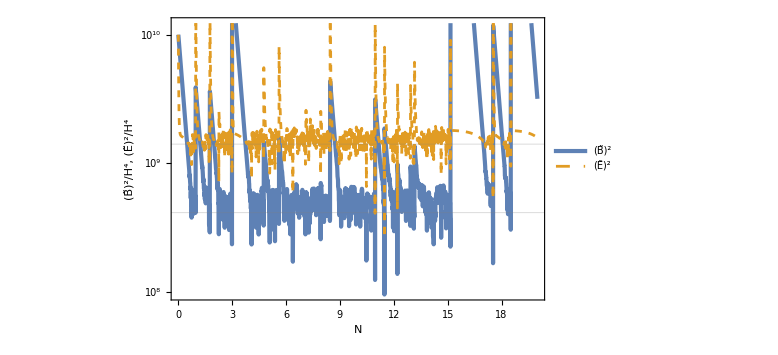

```mathematica
LogPlot[{BAmp[t]/HH^4,EAmp[t]/HH^4},{t,0,Nf},GridLines->{None,{BvarEx[SigmaIRint[xi]]/HH^4,Abs[EvarEx[SigmaIRint[xi]]]/HH^4}},PlotStyle->{AbsoluteThickness[3],{AbsoluteThickness[2],Dashed}},FrameLabel->{N,Row[{OverTilde[Style[B,Bold]]^2,"/",Superscript[H,4],",  ",OverTilde[Style["E",Italic,Bold]]^2,"/",Superscript[H,4]}]},PlotLegends->Placed[LineLegend[{OverTilde[Style[B,Bold]]^2,OverTilde[Style["E",Italic,Bold]]^2},LegendMarkerSize->20,LegendLayout->"Row",LegendFunction->(Framed[#,Background->White]&)],{0.8,0.15}]]
```

```mathematica
SigmaSol[t_]=SigmaEB[Sqrt[EAmp[t]],Sqrt[BAmp[t]]];
```

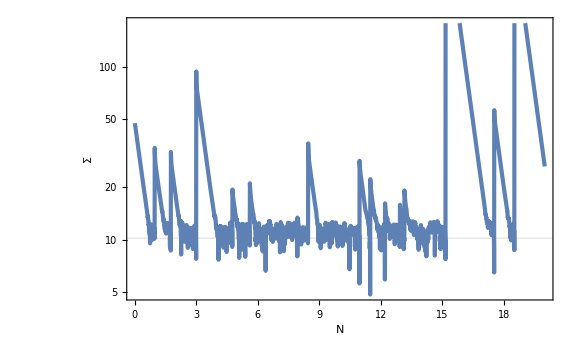

```mathematica
LogPlot[SigmaSol[t],{t,0,Nf},GridLines->{None,{SigmaIRint[xi]}},FrameLabel->{N,Σ}]
```

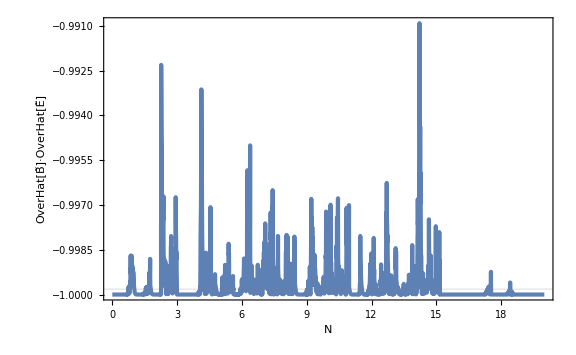

```mathematica
Plot[NormB[t].NormE[t],{t,0,Nf},PlotRange->Full,FrameLabel->{N,OverHat[OverTilde[Style[B,Bold]]]·OverHat[OverTilde[Style["E",Italic,Bold]]]},GridLines->{None,{Re[EdotBNorm[Sigma]]}}]
```

```mathematica
Nplot=9;
ParametricPlot3D[{NormB[t],NormE[t]},{t,Nplot,Nplot+1},AxesLabel->{x,y,z},PlotLegends->Placed[{OverHat[OverTilde[Style[B,Bold]]],OverHat[OverTilde[Style["E",Italic,Bold]]]},{0.1,0.1}],PlotLabel->Style[Row[{N==Nplot,"–",Nplot+1}],Black,Large,FontFamily->"Palatino"]]
```

-Graphics-

```mathematica
MolTheta[phi_]:=theta/.FindRoot[π Sin[phi]==Sin[2theta]+2theta,{theta,0}]
MolPoint[lambda_,phi_]:={lambda Cos[MolTheta[phi]],π/2 Sin[MolTheta[phi]]}
```

```mathematica
lambdaB[t_]=Sign[Bsol[t][[2]]]ArcCos[(Bsol[t][[1]])/(√((Bsol[t][[1]])^2+(Bsol[t][[2]])^2))];
phiB[t_]=ArcSin[NormB[t][[3]]];
MolB[t_]:=MolPoint[lambdaB[t],phiB[t]]
lambdaE[t_]=Sign[Esol[t][[2]]]ArcCos[(Esol[t][[1]])/(√((Esol[t][[1]])^2+(Esol[t][[2]])^2))];
phiE[t_]=ArcSin[NormE[t][[3]]];
MolE[t_]:=MolPoint[lambdaE[t],phiE[t]]
```

```mathematica
MolLongList=Table[MolPoint[lambda,phi],{lambda,-π,π,π/18},{phi,-π/2,π/2,π/180}];//AbsoluteTiming
MolLatList=Table[MolPoint[lambda,phi],{phi,-π/2,π/2,π/18},{lambda,-π,π,π/180}];//AbsoluteTiming
MolFrameList={Table[MolPoint[-π,phi],{phi,-π/2,π/2,π/180}],Table[MolPoint[π,phi],{phi,-π/2,π/2,π/180}]};
```

{7.46802,Null}

{7.05193,Null}

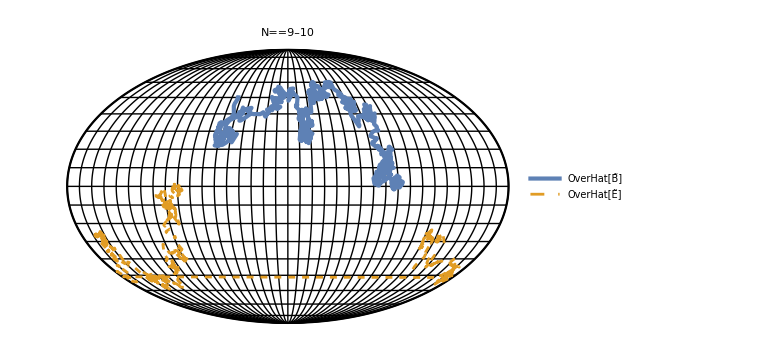

```mathematica
Nplot=9;
Show[ListPlot[MolLongList,PlotStyle->{{Thin,Black}},Frame->False,Axes->False],ListPlot[MolLatList,PlotStyle->{{Thin,Black}}],ListPlot[MolFrameList,PlotStyle->{Black}],ParametricPlot[{MolB[t],MolE[t]},{t,Nplot,Nplot+1},PlotStyle->{AbsoluteThickness[3],{AbsoluteThickness[2],Dashed}},PlotLegends->Placed[LineLegend[{OverHat[OverTilde[Style[B,Bold]]],OverHat[OverTilde[Style["E",Italic,Bold]]]},LegendMarkerSize->20,LabelStyle->Directive[Black,FontSize->20,FontFamily->"Palatino"],LegendFunction->(Framed[#,RoundingRadius->4,Background->White]&)],{0.1,0.2}]],PlotLabel->Style[Row[{N==Nplot,"–",Nplot+1}],Black,Large,FontFamily->"Palatino"],LabelStyle->Directive[Black]]
```

### xi = 15

```mathematica
xi=15;
gamma=2xi;
kappa=kmaxint[xi]
```

2.07049

```mathematica
HH=10^-5;
```

```mathematica
SigmaMax=100;
```

set upper bound for Sigma for a safe simulation

```mathematica
SigmaEB[EE_,BB_]=Min[ee^3 BB/(6 π^2 HH^2)Coth[(π BB)/EE],SigmaMax];
```

```mathematica
WW[x_]=WhittakerW[-I xi,1/2,-2I x];
WS[x_,Sg_]=WhittakerW[-I xi,(1+Sg)/2,-2I x];
MS[x_,Sg_]=WhittakerM[-I xi,(1+Sg)/2,-2I x];
Wp[x_]=D[WW[x], x]//Simplify;
WSp[x_,Sg_]=D[WS[x,Sg], x]//Simplify;
MSp[x_,Sg_]=D[MS[x,Sg], x]//Simplify;
```

```mathematica
c2[Sg_]=gamma^(-Sg/2)Gamma[1+I xi+Sg/2]/(2I Gamma[Sg+2])(Wp[x]MS[x,Sg]-WW[x]MSp[x,Sg]-Sg/(2gamma)WW[x]MS[x,Sg])/.{x->gamma};
c1[Sg_]=-gamma^(-Sg/2)Gamma[1+I xi+Sg/2]/(2I Gamma[Sg+2])(Wp[x]WS[x,Sg]-WW[x]WSp[x,Sg]-Sg/(2gamma)WW[x]WS[x,Sg])/.{x->gamma};
```

```mathematica
XX[Sg_]=c1[Sg]MS[kappa,Sg]+c2[Sg]WS[kappa,Sg];
YY[Sg_]=c1[Sg]MSp[kappa,Sg]+c2[Sg]WSp[kappa,Sg]+Sg/(2kappa)(c1[Sg]MS[kappa,Sg]+c2[Sg]WS[kappa,Sg]);
```

```mathematica
RS[Sg_]=1/(√(Abs[XX[Sg]]^2+Abs[YY[Sg]]^2)){{Abs[YY[Sg]],Abs[XX[Sg]]},{-Abs[XX[Sg]],Abs[YY[Sg]]}};
RT[Sg_]=Transpose[RS[Sg]];
```

```mathematica
Amp[Sg_]=kappa^(4+Sg)HH^4/(12 π^2)Exp[π xi](Abs[XX[Sg]]^2+Abs[YY[Sg]]^2);
```

prepare rotation matrix R and noise amplitude as functions of Sigma (skip it if you already have data)

```mathematica
ListRT12=ParallelTable[{10^logSg,RT[10^logSg][[1,2]]},{logSg,-2,2,1/100}];//AbsoluteTiming
ListRT22=ParallelTable[{10^logSg,RT[10^logSg][[2,2]]},{logSg,-2,2,1/100}];//AbsoluteTiming
ListAmp=ParallelTable[{10^logSg,Amp[10^logSg]},{logSg,-2,2,1/100}];//AbsoluteTiming
```

{1412.59,Null}

{1407.5,Null}

{241.288,Null}

```mathematica
Export["RT12xi15_consistentkappa.dat",ListRT12];
Export["RT22xi15_consistentkappa.dat",ListRT22];
Export["Ampxi15_consistentkappa.dat",ListAmp];
```

```mathematica
ListRT12=Import["RT12xi15_consistentkappa.dat"]//ToExpression;
ListRT22=Import["RT22xi15_consistentkappa.dat"]//ToExpression;
ListAmp=Import["Ampxi15_consistentkappa.dat"]//ToExpression;
```

```mathematica
RT12int[Sg_]=Interpolation[ListRT12][Sg];
RT22int[Sg_]=Interpolation[ListRT22][Sg];
Ampint[Sg_]=Max[Interpolation[ListAmp][Sg],0];
```

```mathematica
SDE={ⅆBx[t]+2 Bx[t]ⅆt==RT12int[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]] Sqrt[Ampint[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]]]ⅆwx[t],ⅆBy[t]+2 By[t]ⅆt==RT12int[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]] Sqrt[Ampint[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]]]ⅆwy[t],ⅆBz[t]+2 Bz[t]ⅆt==RT12int[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]] Sqrt[Ampint[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]]]ⅆwz[t],ⅆEx[t]+2 Ex[t]ⅆt+2xi Bx[t]ⅆt+SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]] Ex[t]ⅆt==RT22int[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]] Sqrt[Ampint[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]]]ⅆwx[t],ⅆEy[t]+2 Ey[t]ⅆt+2xi By[t]ⅆt+SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]] Ey[t]ⅆt==RT22int[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]] Sqrt[Ampint[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]]]ⅆwy[t],ⅆEz[t]+2 Ez[t]ⅆt+2xi Bz[t]ⅆt+SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]] Ez[t] ⅆt==RT22int[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]] Sqrt[Ampint[SigmaEB[Norm[{Ex[t],Ey[t],Ez[t]}],Norm[{Bx[t],By[t],Bz[t]}]]]]ⅆwz[t]};
```

```mathematica
proc=ItoProcess[SDE,{Bx[t],By[t],Bz[t],Ex[t],Ey[t],Ez[t]},{{Bx,By,Bz,Ex,Ey,Ez},{10^-5,0,0,-10^-5,0,0}},t,{wx\[Distributed]WienerProcess[],wy\[Distributed]WienerProcess[],wz\[Distributed]WienerProcess[]}];
```

```mathematica
Nf=20;
```

```mathematica
sol=RandomFunction[proc,{0,Nf,0.001}];//AbsoluteTiming
```

{3.8625,Null}

```mathematica
Bsol[t_]={sol["PathComponent",1]["PathFunction"][t],sol["PathComponent",2]["PathFunction"][t],sol["PathComponent",3]["PathFunction"][t]};
Esol[t_]={sol["PathComponent",4]["PathFunction"][t],sol["PathComponent",5]["PathFunction"][t],sol["PathComponent",6]["PathFunction"][t]};
```

```mathematica
BAmp[t_]=Norm[Bsol[t]]^2;
NormB[t_]=Bsol[t]/Norm[Bsol[t]];
EAmp[t_]=Norm[Esol[t]]^2;
NormE[t_]=Esol[t]/Norm[Esol[t]];
```

```mathematica
PBB[Sg_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)Abs[c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg]]^2/.{x->kappa};
PEE[Sg_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)Abs[c1[Sg]MSp[x,Sg]+c2[Sg]WSp[x,Sg]+Sg/(2x)(c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg])]^2/.{x->kappa};
PBE[Sg_]=HH^4/(4 π^2)Exp[π xi] x^(4+Sg)(c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg]) Conjugate[c1[Sg]MSp[x,Sg]+c2[Sg]WSp[x,Sg]+Sg/(2x)(c1[Sg]MS[x,Sg]+c2[Sg]WS[x,Sg])]/.{x->kappa};
PEB[Sg_]=Conjugate[PBE[Sg]];
BvarEx[Sg_]=1/4 PBB[Sg];
EvarEx[Sg_]=1/(4+2Sg)PEE[Sg]-xi/((2+Sg)(4+Sg))(PBE[Sg]+PEB[Sg])+xi^2/((2+Sg)(4+Sg))PBB[Sg];
EdotBNorm[Sg_]=(1/(4+Sg)Re[PEB[Sg]]-xi/(2(4+Sg))PBB[Sg])/(√(BvarEx[Sg]EvarEx[Sg]));
```

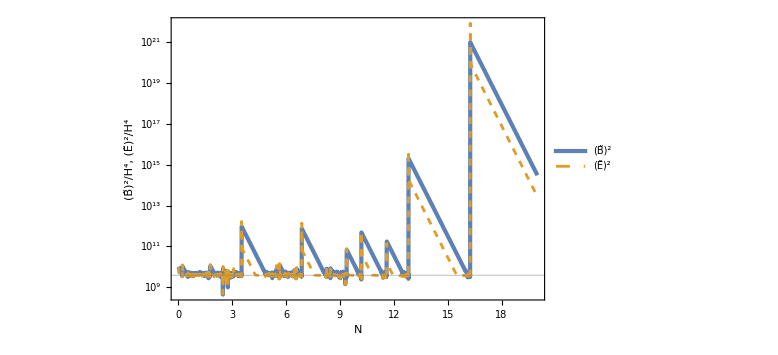

```mathematica
LogPlot[{BAmp[t]/HH^4,EAmp[t]/HH^4},{t,0,Nf},GridLines->{None,{BvarEx[SigmaIRint[xi]]/HH^4,Abs[EvarEx[SigmaIRint[xi]]]/HH^4}},PlotStyle->{AbsoluteThickness[3],{AbsoluteThickness[2],Dashed}},FrameLabel->{N,Row[{OverTilde[Style[B,Bold]]^2,"/",Superscript[H,4],",  ",OverTilde[Style["E",Italic,Bold]]^2,"/",Superscript[H,4]}]},PlotLegends->Placed[LineLegend[{OverTilde[Style[B,Bold]]^2,OverTilde[Style["E",Italic,Bold]]^2},LegendMarkerSize->20,LegendLayout->"Row",LegendFunction->(Framed[#,Background->White]&)],{0.8,0.15}]]
```

```mathematica
SigmaSol[t_]=SigmaEB[Sqrt[EAmp[t]],Sqrt[BAmp[t]]];
```

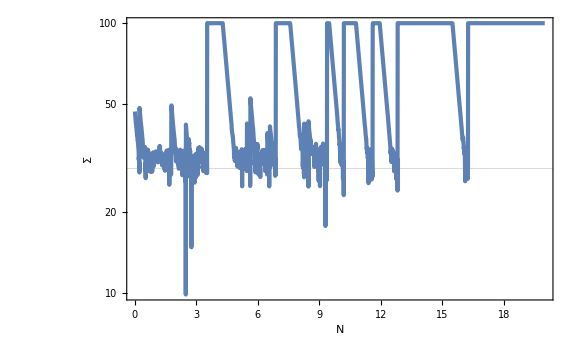

```mathematica
LogPlot[SigmaSol[t],{t,0,Nf},GridLines->{None,{SigmaIRint[xi]}},FrameLabel->{N,Σ}]
```

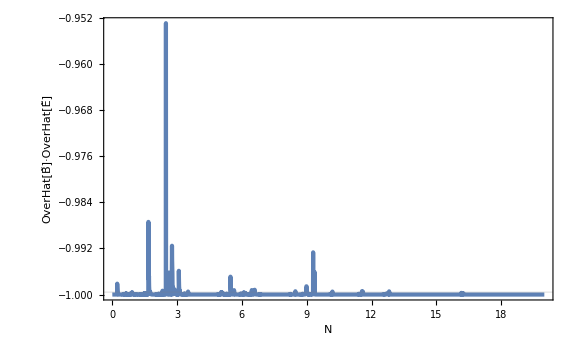

```mathematica
Plot[NormB[t].NormE[t],{t,0,Nf},PlotRange->Full,FrameLabel->{N,OverHat[OverTilde[Style[B,Bold]]]·OverHat[OverTilde[Style["E",Italic,Bold]]]},GridLines->{None,{Re[EdotBNorm[Sigma]]}}]
```

```mathematica
Nplot=2;
ParametricPlot3D[{NormB[t],NormE[t]},{t,Nplot,Nplot+1},AxesLabel->{x,y,z},PlotLegends->Placed[{OverHat[OverTilde[Style[B,Bold]]],OverHat[OverTilde[Style["E",Italic,Bold]]]},{0.1,0.1}],PlotLabel->Style[Row[{N==Nplot,"–",Nplot+1}],Black,Large,FontFamily->"Palatino"]]
```

-Graphics-

```mathematica
MolTheta[phi_]:=theta/.FindRoot[π Sin[phi]==Sin[2theta]+2theta,{theta,0}]
MolPoint[lambda_,phi_]:={lambda Cos[MolTheta[phi]],π/2 Sin[MolTheta[phi]]}
```

```mathematica
lambdaB[t_]=Sign[Bsol[t][[2]]]ArcCos[(Bsol[t][[1]])/(√((Bsol[t][[1]])^2+(Bsol[t][[2]])^2))];
phiB[t_]=ArcSin[NormB[t][[3]]];
MolB[t_]:=MolPoint[lambdaB[t],phiB[t]]
lambdaE[t_]=Sign[Esol[t][[2]]]ArcCos[(Esol[t][[1]])/(√((Esol[t][[1]])^2+(Esol[t][[2]])^2))];
phiE[t_]=ArcSin[NormE[t][[3]]];
MolE[t_]:=MolPoint[lambdaE[t],phiE[t]]
```

```mathematica
MolLongList=Table[MolPoint[lambda,phi],{lambda,-π,π,π/18},{phi,-π/2,π/2,π/180}];//AbsoluteTiming
MolLatList=Table[MolPoint[lambda,phi],{phi,-π/2,π/2,π/18},{lambda,-π,π,π/180}];//AbsoluteTiming
MolFrameList={Table[MolPoint[-π,phi],{phi,-π/2,π/2,π/180}],Table[MolPoint[π,phi],{phi,-π/2,π/2,π/180}]};
```

{7.46802,Null}

{7.05193,Null}

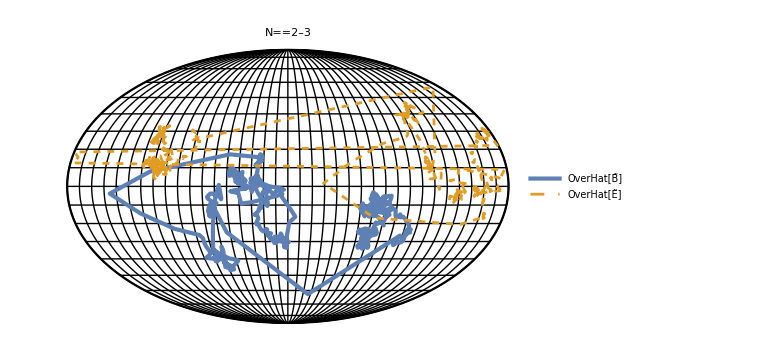

```mathematica
Nplot=2;
Show[ListPlot[MolLongList,PlotStyle->{{Thin,Black}},Frame->False,Axes->False],ListPlot[MolLatList,PlotStyle->{{Thin,Black}}],ListPlot[MolFrameList,PlotStyle->{Black}],ParametricPlot[{MolB[t],MolE[t]},{t,Nplot,Nplot+1},PlotStyle->{AbsoluteThickness[3],{AbsoluteThickness[2],Dashed}},PlotLegends->Placed[LineLegend[{OverHat[OverTilde[Style[B,Bold]]],OverHat[OverTilde[Style["E",Italic,Bold]]]},LegendMarkerSize->20,LabelStyle->Directive[Black,FontSize->20,FontFamily->"Palatino"],LegendFunction->(Framed[#,RoundingRadius->4,Background->White]&)],{0.1,0.2}]],PlotLabel->Style[Row[{N==Nplot,"–",Nplot+1}],Black,Large,FontFamily->"Palatino"],LabelStyle->Directive[Black]]
```